## Design Space Analysis

```mathematica
ClearAll["Global`*"]
```

This mathematica notebook will do the analysis shown in [1], [2], and [3].

### Module 1: Properties

```mathematica
(*Module 1 and 2 expands and reduces log equations (log properties)
Input: Log Expression
Output: Expanded/Reduced LogExpression
*)
```

```mathematica
expandLog[expr_]:=Block[{rule1,rule2,rule3,a,b,x},rule1=Log[a_*b_]->Log[a]+Log[b];
rule2=Log[a_^x_]->x*Log[a];
rule3 = Log[a_/b_]-> Log[a]-Log[b];
(expr/.rule1)/.rule2/.rule3];
reduceLog[expr_]:=Block[{rule1,rule2,rule3,a,b,x},rule1=Log[a_]+Log[b_]-> Log[a*b];
rule2=x_*Log[a_]->Log[a^x];
rule3 = Log[a_]-Log[b_]->  Log[a/b];
(expr/.rule1)/.rule2/.rule3];
```

### Module 2: Obtaining Dominant S-Systems, Logged Steady States, and Boundary Inequalities

```mathematica
(*Module 1 creates a matrix of all the possible dominant S-Systems
Input: True ODE system (excluding rate of change), parameter Assumptions, Nested parameter (How many times you want to apply expandLog function)
		Note: ODE independent variable should be Subscript[x, 0][t],Subscript[x, 1][t],...,Subscript[x, N][t]
			  Denominators are defined to be a new variable and added to equations
Output: Matrix of all possible Dominant S-Systems
*)
```

```mathematica
ParameterAssumptions[parametersofinterest_,system_]:=Block[{variablesofinterest,combinedinterest},
variablesofinterest = Table[Subscript[x, i][t],{i,0,Length[system]-1}];
combinedinterest = Thread[Join[parametersofinterest,variablesofinterest]>0]]
```

```mathematica
DominantSubSystems[odeSystem_,paramConstraints_,nested_]:=Block[{ODELength,SystemTuples,DominantSubSystemvars,PositiveNegatives,SteadyStateEquations,LogSolutions,individuals,MapODELength,VariablesOfChoice,VariablesOfChoiceMapLength,InequalitiesNotEvaluated,DominantSubSystemvarsOriginal},
ODELength = Length[odeSystem];
individuals= Table[Level[odeSystem[[i]],1],{i,ODELength}];
PositiveNegatives = Thread[{Flatten[Table[Table[If[Refine[(individuals[[i,j]])>0,paramConstraints],individuals[[i,j]],##&[]],{i,{loop}},{j,1,Length[individuals[[loop]]]}],{loop,1,ODELength}],1],Flatten[Table[Table[If[Refine[(individuals[[i,j]])<0,paramConstraints],individuals[[i,j]],##&[]],{i,{loop}},{j,1,Length[individuals[[loop]]]}],{loop,1,ODELength}],1]}];
SystemTuples = Map[Tuples,PositiveNegatives];
DominantSubSystemvars = Tuples[SystemTuples];
DominantSubSystemvarsOriginal = DominantSubSystemvars;
(*Log steady state of Dominant S-Systems*)
DominantSubSystemvars[[All,All,2]] = -DominantSubSystemvars[[All,All,2]];
SteadyStateEquations = Map[Map[Apply[Equal]],Log[DominantSubSystemvars]];
LogSolutions =Table[Solve[Nest[expandLog,SteadyStateEquations[[i]],nested],Table[Log[Subscript[x, jj][t]],{jj,0,ODELength-1}]],{i,Length[SteadyStateEquations]}];
(*S-Systems and Log Steady State output*)

(*Inequalities*)
MapODELength = Map[Length,odeSystem];
PositiveNegatives[[All,2]] = -PositiveNegatives[[All,2]];
VariablesOfChoice = Log[Flatten[Table[If[Length[PositiveNegatives[[i,j]]]>1,PositiveNegatives[[i,j]],##&[]],{i,1,Length[PositiveNegatives]},{j,1,2}],1]];
VariablesOfChoiceMapLength = Map[Length,VariablesOfChoice];
InequalitiesNotEvaluated = Map[Flatten,Tuples[Table[If[VariablesOfChoiceMapLength[[i]]== 2,Permutations[Apply[Greater,VariablesOfChoice[[i]]],{2}],Partition[Permutations[Apply[Greater,VariablesOfChoice[[i]]],{2}],VariablesOfChoiceMapLength[[i]]-1]],{i,1,Length[VariablesOfChoiceMapLength]}]]];

(*Output Solution {S-System,Log Steady State,Inequalities Not Evaluated}*)
{Map[Map[Apply[Plus]],DominantSubSystemvarsOriginal],LogSolutions,Nest[expandLog,InequalitiesNotEvaluated,nested]}
]
```

### Module 3: Checking Stability of Dominant Sub Systems

```mathematica
Eigenvals[Ssystems_,SteadyState_]:=Block[{LengthOfSystem,jacob,eiegenvals,eigenvals},
jacob =Table[Table[Table[D[Ssystems[[k,j]],Subscript[x, i][t]],{i,0,Length[Ssystems[[k]]]-1}],{j,1,Length[Ssystems[[k]]]}],{k,Length[Ssystems]}];

Table[Eigenvalues[jacob[[i]]]/.SteadyState[[i]],{i,1,Length[SteadyState]}]//N
];
```

```mathematica
CheckingStability[Inequalities_,params_,evalsVector_,pops_] := Block[{EvaluatedEVals,instance,parAssump,additionalparAssump},
(*parAssump=ParameterAssumptions[params,2];
additionalparAssump = {p0<1, p1<1,q1<1,p1+q1<1};*)
instance = Flatten[Table[FindInstance[Inequalities[[i]],
params,Reals],{i,1,Length[Inequalities]}],1];
EvaluatedEVals = Table[ N[evalsVector[[i]]/.instance[[i]]][[1;;pops]],{i,1Length[instance]}];
Table[
If[Apply[And,Thread[Re[EvaluatedEVals[[jj]]]<0]]&&  Apply[Or,Thread[Im[EvaluatedEVals[[jj]]]≠0]] (*Stable Spiral*),
Apply[And,Thread[Re[EvaluatedEVals[[jj]]]<0]]&&  Apply[And,Thread[Im[EvaluatedEVals[[jj]]]== 0]] (*Stable Node*),"Stable Node",
If[Apply[And,Thread[Re[EvaluatedEVals[[jj]]]<0]]&&  Apply[Or,Thread[Im[EvaluatedEVals[[jj]]]≠0]] (*Stable Spiral*),"Stable Spiral",
If[Apply[And,Thread[Re[EvaluatedEVals[[jj]]]>0]]&&  Apply[And,Thread[Im[EvaluatedEVals[[jj]]]== 0]] (*Unstable Node*),"Unstable Node",

If[Apply[And,Thread[Re[EvaluatedEVals[[jj]]]>0]]&&  Apply[Or,Thread[Im[EvaluatedEVals[[jj]]]≠0]] (*Unstable Spiral*),"Unstable Spiral","Unknown"
]
]
]
],{jj,Length[EvaluatedEVals]}]
];(*End Block*)
```

```mathematica
Stability[Ssystems_,Inequalities_,params_,pops_,sstate_]:=Block[{evalVector},
evalVector = Eigenvals[Ssystems,sstate];
CheckingStability[Inequalities,params,evalVector,pops] 
]
```

### Module 4: Design Space

```mathematica
KeepingTrackofDominantSystems[logss_] :=Block[{},
Table[If[(Length[logss[[i]]]>0)||(logss[[i]]==  {False}),i,##&[]],{i,1,Length[logss]}]
]
```

```mathematica
DesignSpace[ODEsystem_,params_,nested_] := Block[{SSystemsLogSteadyStatesInequalties,SSystem,InequaltiesNotEvaluated,BoundaryDesign,paramConstraints,NonEmptyIndexCheck1,NonEmptyIndexCheck2,LogSteadyStateUpdated,SteadyStates,LogSteadyStateUpdatedUpdated,LogSteadyState,LogSSindexofInterest, LenLogSS},
paramConstraints = ParameterAssumptions[params,ODEsystem];
SSystemsLogSteadyStatesInequalties = DominantSubSystems[ODEsystem,paramConstraints,nested];
SSystem = SSystemsLogSteadyStatesInequalties[[1]];
LogSteadyState = SSystemsLogSteadyStatesInequalties[[2]];
LenLogSS = Map[Map[Length],LogSteadyState];
LogSSindexofInterest = Table[If[LenLogSS[[i]]=={Length[ODEsystem]},i,##&[]],{i,Length[LogSteadyState]}];
LogSteadyState = LogSteadyState[[LogSSindexofInterest]];
InequaltiesNotEvaluated = SSystemsLogSteadyStatesInequalties[[3]][[LogSSindexofInterest]];
SSystem = SSystem[[LogSSindexofInterest]];
NonEmptyIndexCheck1 = KeepingTrackofDominantSystems[LogSteadyState];
LogSteadyStateUpdated = LogSteadyState[[NonEmptyIndexCheck1]];
BoundaryDesign = Map[DeleteCases[False],Map[Map[Apply[And]],Table[InequaltiesNotEvaluated[[i]]/.LogSteadyState[[i]],{i,NonEmptyIndexCheck1}]]//FullSimplify];
NonEmptyIndexCheck2 = NonEmptyIndexCheck1[[KeepingTrackofDominantSystems[BoundaryDesign]]];
LogSteadyStateUpdatedUpdated = LogSteadyState[[NonEmptyIndexCheck2]];
SteadyStates = Map[Map[Map[Exp]],Nest[reduceLog,Flatten[LogSteadyStateUpdatedUpdated,1],20]];
{SSystem[[NonEmptyIndexCheck2]],BoundaryDesign[[NonEmptyIndexCheck2]],LogSteadyStateUpdatedUpdated,SteadyStates}
]
```

### Module 5: Plotting LogLogRegionPlot

```mathematica
logLogRegionPlot[rplot_]:=Module[{pts,pgon},pts=Cases[Normal@rplot,Line[a__]:>a,Infinity];
pgon={EdgeForm[],Directive[RGBColor[0.3,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[0.3]],Cases[Normal@rplot,Polygon[_],Infinity]};
ListLogLogPlot[pts,Joined->True,Frame->True,PlotRange->All,AspectRatio->1,Axes->False,PlotStyle->Blue,Epilog->(pgon/.{x_,y_?NumericQ}:>Log@{x,y})]]
```

### Example:

```mathematica
odesystem ={(2 p0/(Subscript[x, 4][t])-1)eta1/(Subscript[x, 5][t]) Subscript[x, 0][t],
		2(1-p0/(Subscript[x, 4][t]))eta1/(Subscript[x, 5][t]) Subscript[x, 0][t]+(2 p1/(Subscript[x, 6][t])-1)eta2/(Subscript[x, 8][t])Subscript[x, 1][t],
		2 q1/(Subscript[x, 7][t]) eta2/(Subscript[x, 8][t])Subscript[x, 1][t] - dL Subscript[x, 2][t],
		2(1-p1/(Subscript[x, 6][t])-q1/(Subscript[x, 7][t]))eta2/(Subscript[x, 8][t])Subscript[x, 1][t]- dM Subscript[x, 3][t],
		1+gam1*Subscript[x, 1][t]-Subscript[x, 4][t],
		1+gam2*Subscript[x, 0][t]-Subscript[x, 5][t],
                  1+gam3*Subscript[x, 3][t]-Subscript[x, 6][t],
		1+gam4* Subscript[x, 3][t]-Subscript[x, 7][t],
		1+gam5* Subscript[x, 0][t]-Subscript[x, 8][t]}//Expand;
```

```mathematica
dsa = DesignSpace[odesystem,{p0,eta1, p1, eta2,q1,dL,dM, gam1, gam2, gam3,gam4, gam5},20];
```

```mathematica
SSystems = dsa[[1]];
Boundaries = dsa[[2]];
SState = dsa[[4]];
```

## Design space

Design space for parameter set used for Passague experiment + CML development+therapy

```mathematica
Boundaries/.{p0->0.54,p1->0.42,q1->0.105,dM->0.17,dL->0.05,gam2->.445841266*10^-5,gam4->1.84014128*10^-10,eta1->0.3749,eta2->1.309, gam5->1.39464368*10^-8}//FullSimplify
```

{{11.6865+Log[gam1]>0&&Log[gam1]>2.81133+Log[gam3]},{False},{False},{False},{Log[gam1]<2.81133+Log[gam3]&&11.6865+Log[gam1]>0},{False},{False},{False},{11.6865+Log[gam1]<0&&14.4979+Log[gam3]<0},{False},{14.4979+Log[gam3]>0&&11.6865+Log[gam1]<0},{False},{False},{False},{False},{False},{False},{False},{False},{False},{False},{False}}

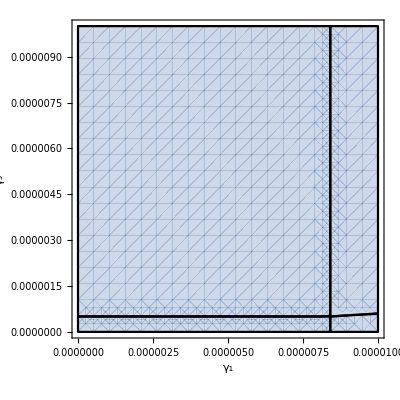

```mathematica
graph = Show[Table[RegionPlot[Boundaries[[i]]/.{p0->0.54,p1->0.42,q1->0.105,dM->0.17,dL->0.05,gam2->.445841266*10^-5,gam4->1.84014128*10^-10,eta1->0.3749,eta2->1.309, gam5->1.39464368*10^-8},{gam1,0,.00001},{gam3,0,.00001},FrameLabel->{"γ_1","γ_3"},BoundaryStyle->Black],{i,{1,5,9,11}}]]
```

```mathematica
nds = NDSolve[{x0'[t]==(2 p0/(1+gam1*x1[t])-1)eta1/(1+gam2 x0[t]) x0[t],
			x1'[t]==2(1-p0/(1+gam1*x1[t]))eta1/(1+gam2 x0[t]) x0[t]+(2 p1/(1+gam3 x3[t])-1)eta2/(1+gam5 x0[t])x1[t],
			x2'[t]==2 q1/(1+gam4 x3[t])eta2/(1+gam5 x0[t])x1[t]-dL x2[t],
			x3'[t]==2*(1-p1/(1+gam3 x3[t])- q1/(1+gam4 x3[t]))eta2/(1+gam5 x0[t])x1[t]-dM x3[t],
			x0[0]==1.*10^4, x1[0]==1.*10^4, x2[0]==1.*10^4, x3[0]==1.*10^4}/.{p0->0.54,p1->0.42,q1->0.105,dM->0.17,dL->0.05,gam2->.445841266*10^-5,gam4->1.84014128*10^-10,eta1->0.3749,eta2->1.309, gam5->1.39464368*10^-8}/.samplingdomain[[100]],{x0[t],x1[t],x2[t],x3[t]},{t,0,1000}];
Plot[{x0[t]/.nds, x1[t]/.nds,x2[t]/.nds,x3[t]/.nds},{t,0,1000},PlotRange->All, PlotStyle->{Black, Blue, Green, Cyan}]
```

```mathematica
Manipulate[nds = NDSolve[{x0'[t]==(2 p0/(1+gam1*x1[t])-1)eta1/(1+gam2 x0[t]) x0[t],
			x1'[t]==2(1-p0/(1+gam1*x1[t]))eta1/(1+gam2 x0[t]) x0[t]+(2 p1/(1+gam3 x3[t])-1)eta2/(1+gam5 x0[t])x1[t],
			x2'[t]==2 q1/(1+gam4 x3[t])eta2/(1+gam5 x0[t])x1[t]-dL x2[t],
			x3'[t]==2*(1-p1/(1+gam3 x3[t])- q1/(1+gam4 x3[t]))eta2/(1+gam5 x0[t])x1[t]-dM x3[t],
			x0[0]==1.*10^4, x1[0]==1.*10^4, x2[0]==1.*10^4, x3[0]==1.*10^4}/.{p0->0.54,p1->0.42,q1->0.105,dM->0.17,dL->0.05,gam2->.445841266*10^-5,gam4->1.84014128*10^-10,eta1->0.3749,eta2->1.309, gam5->1.39464368*10^-8}/.{gam1->gam1vary, gam3->gam3vary},{x0[t],x1[t],x2[t],x3[t]},{t,0,tend}];
{Plot[{x0[t]/.nds, x1[t]/.nds,x2[t]/.nds,x3[t]/.nds},{t,0,tend},PlotRange->All, PlotStyle->{Black, Blue, Green, Cyan}],Show[graph,Epilog->{PointSize->Large,Point[{{gam1vary,gam3vary}}]}]},
{gam1vary,0.00002},{gam3vary,1.*^-6},{tend,1000}]
```

Code was last reviewed September 12, 2019.
For questions, please contact abdoni@uci.edu